# Chapter 1: Using and Understanding Mathematica

## Main aim of this chapter is to provide reader with introduction to basic commands of Mathematica and motivation to use it

## So let’s start with a very basic calculation

```mathematica
N[Sqrt[2],10](*Sqrt is the square root function and N[,(?)] a number in the second bracket will give that many number of digits after the decimal point *)
```

1.414213562

Interestingly Mathematica has very useful shortcut keys 
%  → the last generated result
%%  → the next to last generated result
% n → the result in the output line n (look at the left side just below the command and it will be self-explanatory)

```mathematica
%
```

1.414213562

```mathematica
%^2
```

2.

```mathematica
%5
```

2.

## Alright let’s move on to the next section where we will do some symbolic maths

Here is the list of few commands that we are going to use

Expand[ ] : It will expand the given compact expression 
Factor[ ]: It  will write expression as products of minimal factors 
Simplify[ ]: It will simplify the expression 
FullSimplify[ ]: It is just comprehensive version of Simplify (Honestly people just use this command when simplify doesn’t work lol )
PowerExpand[ ]: It transform normal expression in the form of powers 

There is one more command that is extensively used 
(Any mathematical function) /. (variable) → value  and the function will take that value in place of variable. 

Let’s move on to the playground!

```mathematica
x^2 -2x+1
```

1-2 x+x^2

```mathematica
x^2 -2x+1 /.x-> y+2
```

1-2 (2+y)+(2+y)^2

```mathematica
Expand[%]
```

1+2 y+y^2

```mathematica
Factor[%]
```

(1+y)^2

```mathematica
Simplify[%11]
```

(1+y)^2

```mathematica
PowerExpand[(x y)^12]
```

x^12 y^12

At this point a lot you must be thinking, wow this is really cool Mathematica is too smart or genius as a program but actually sometimes it cannot see some of most obvious things

```mathematica
f = x^2 + y^2
```

x^2+y^2

```mathematica
f/.{x-> Cos[t], y->Sin[t]} (*Before exicuting this line, what do you expect to be your solution? 1 right! Now exicute the command*)
```

Cos[t]^2+Sin[t]^2

Voila! So now what, is Mathematica dumb? no, it’s just that Mathematica does not automatically remember the identities, so in these type of cases where we have an identity we should be using few “reminders” function. 

TrigExpand[ ] → Expands the expression into the sum of terms 
TrigFactor[ ] → Write the expression into as products of terms 
TrigReduce[ ] → Uses the trigonometric identities

```mathematica
TrigReduce[%](*See now we are getting the expected outcome*)
```

1

```mathematica
g = Sin[x+y]
```

Sin[x+y]

```mathematica
TrigExpand[g]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

```mathematica
h = %/.{y-> 2x}
```

Cos[2 x] Sin[x]+Cos[x] Sin[2 x]

```mathematica
TrigExpand[h]
```

3 Cos[x]^2 Sin[x]-Sin[x]^3

```mathematica
TrigFactor[%]
```

(1+2 Cos[2 x]) Sin[x]

```mathematica
TrigReduce[%]
```

Sin[3 x]

I would suggest the reader to play around with these functions to a better understanding to them.

Moving forward, let’s shift our discussion to rational expressions and discuss the functions that might come in handy. 

Forward[ ] : Reduce the expression to product of factors 
Together[ ] : Placing all terms over a common denominator 
Apart[ ] : Exactly opposite of Together function 
Cancel[ ]: Cancels out the common factors from numerators and denominators

```mathematica
f = (x^3+3x^2 +3x +1)/(x^3 + 2x^2 +x) (*Choose any random expression*)
```

(1+3 x+3 x^2+x^3)/(x+2 x^2+x^3)

```mathematica
Apart[f]
```

1+1/x

```mathematica
Together[f]
```

(1+x)/x

```mathematica
Cancel[f]
```

(1+x)/x

Then comes functions that are useful for separating different parts of an expression, since the function’s names are self-explanatory I am directly going to show you how it works

```mathematica
Numerator[f]
```

1+3 x+3 x^2+x^3

```mathematica
Denominator[f]
```

x+2 x^2+x^3

```mathematica
Part[f,2]
```

1+3 x+3 x^2+x^3

```mathematica
Coefficient[Numerator[f],x^2] (*It will give the coefficient of the algebraic expression*)
```

3

Mathematica has also a built-in summation expression 

From now on we will do one thing, I will directly show the example of a Mathematica function and it’s you are confused about the terminology of that function then you can use ?(That function)

```mathematica
?Sum
```

```mathematica
Sum[1/k^2,{k,1,Infinity}](*A very famous summation*)
```

π^2/6

## Calculus in Mathematica

Mathematica’s symbolic engine makes it a powerful tool for analytic calculations in physics.
We’ll explore how to use it for differentiation, integration, and series expansions both symbolically and numerically.

For differentiation, we are going to use following commands 
D[f,x] : (∂f)/(∂x)
D[f,x1,x2,...] : (∂f)/(∂x_1)(∂f)/(∂x_2)...

```mathematica
?D
```

```mathematica
D[x^2,x]
```

2 x

```mathematica
D[Sin[x+y]Exp[x y],x]
```

ⅇ^(x y) Cos[x+y]+ⅇ^(x y) y Sin[x+y]

```mathematica
D[Sin[x+x Exp[Cos[x]]],x](*Take any ugly looking function and mathematica will find the differential for you*)
```

Cos[x+ⅇ^Cos[x] x] (1+ⅇ^Cos[x]-ⅇ^Cos[x] x Sin[x])

Now, we will discuss the integral functions, there two types of integral one is defining where we have to work in a domain (a,b) and other is indefinite.

```mathematica
?Integrate
```

```mathematica
f = x^2 Log[x]
```

x^2 Log[x]

```mathematica
Integrate[f,x]
```

-x^3/9+1/3 x^3 Log[x]

Let’s integrate a Gaussian function

```mathematica
Integrate[Exp[-x^2], {x,0, Infinity}]
```

(√π)/2

It is also familiar to some other very famous integrals

```mathematica
Integrate[Sqrt[1-k Sin[x]^2],x]
```

EllipticE[x,k]

But but but....it is not a magic wand so obviously it cannot do everything analytically

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

```mathematica
N[%]
```

0.783431

## User defined functions

```mathematica
f[x_]:= x+1 (*We can define functions in this form f[x_]*)
```

```mathematica
f[1]
```

2

Let’s do some complicated calculations using this!

```mathematica
f[x_]:=x^2Cos[x] + x Sin[x]
```

```mathematica
f[π]
```

-π^2

```mathematica
f[Exp[y]]
```

ⅇ^(2 y) Cos[ⅇ^y]+ⅇ^y Sin[ⅇ^y]

```mathematica
D[f[Exp[y]],y]
```

3 ⅇ^(2 y) Cos[ⅇ^y]+ⅇ^y Sin[ⅇ^y]-ⅇ^(3 y) Sin[ⅇ^y]

```mathematica
Integrate[f[Exp[y]],{y,0,1}]
```

-Sin[1]+ⅇ Sin[ⅇ]

## Numerical Mathematics

This is one of the most important things researchers use, the reason is you cannot solve every equation analytically that’s where this method comes in handy 

For this part we are going to explore Solve and NSolve

```mathematica
?Solve
```

Let’s start with one of the most fundamental equation we know  The Quadratic Equation

```mathematica
expr = a x^2 + b x + c
```

c+b x+a x^2

```mathematica
Solve[expr == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
expr = 1+x+2x^2 +2x^3 +x^4
```

1+x+2 x^2+2 x^3+x^4

```mathematica
Solve[expr==0,x]
```

{{x→1/2 (-1-√(1-4 (-1)^(1/3)))},{x→1/2 (-1+√(1-4 (-1)^(1/3)))},{x→1/2 (-1-√(1+4 (-1)^(2/3)))},{x→1/2 (-1+√(1+4 (-1)^(2/3)))}}

And to get a numerical answer, we will use NSolve

```mathematica
NSolve[expr,x]
```

{{x→-1.0707-0.758745 ⅈ},{x→-1.0707+0.758745 ⅈ},{x→0.070696-0.758745 ⅈ},{x→0.070696+0.758745 ⅈ}}

```mathematica
f[x]/.sol
```

Let’s make things a bit interesting

```mathematica
Solve[x==Cos[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x==Cos[x],x]

```mathematica
NSolve[x==Cos[x],x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[x==Cos[x],x]

You might be thinking what just happened! Why it can’t solve a simple equation, the reason is it is not algebraic but transcendental equation, for these kind of expressions we have FindRoot function in Mathematica

```mathematica
?FindRoot
```

```mathematica
FindRoot[x==Cos[x],{x,0}]
```

{x→0.739085}

But while using this method one need a prior estimate of the location of the root. It mostly uses Newton’s method for finding root

In undesirable circumstances, Newton’s method may take a large number of successive calculations to get to the root, or it may never reach the root. The default number of successive approximations for Mathematica
is 15. If after 15 trials Mathematica does not get close enough to the root, it gives a warning and prints out the latest approximation. So, in using FindRoot, it is a good idea to have a rough estimate of the root and be
ready to try a different estimate if the first one does not yield results. In case of multiple roots, we can specify the interval in which the root may lie. This is done by using the following

## Plotting using Mathematica

The results of numerical mathematics-and many symbolic manipulations as well-are best conveyed in the form of graphics. Mathematica has a very powerful graphics capability suitable for simple two-dimensional plots as well as complex, multicolored three-dimensional images.

### Simple Plots

```mathematica
?Plot
```

```mathematica
f[x_]:=Exp[-x/10]Sin[x]
```

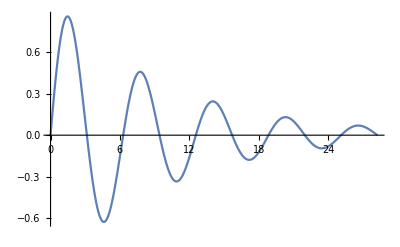

```mathematica
Plot[f[x],{x,0, 9Pi},PlotRange->All](*If you can't see your plot then use this PlotRange function *)
```

### Parametric Plots

?ParametricPlot

One of the most basic parametric equation we know is of circle. 
a point can be described as (Cos[t], Sin[t])



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

We can play around the parametric functions and we can get different shapes

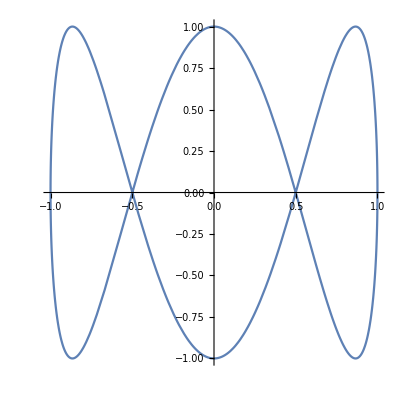

```mathematica
ParametricPlot[{Cos[t],Sin[3t]},{t,0,2Pi}]
```

If you find these marking annoying then you can use Ticks → None to hide them

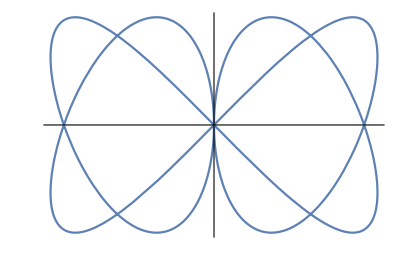

```mathematica
ParametricPlot[{Cos[t]Sin[2t],Cos[2t]Sin[2t]},{t,0,2Pi}, Ticks->None]
```

### Contour and Density Plots

The two-dimensional contour and density plots are less common in the introductory courses. However, they are indispensable in computationally
intensive advanced courses and research areas. A contour plot of f(x, y) is a topographical map of the function. It gives the boundaries of slices cut through the function by planes parallel to the xy-plane. The density plot depicts the value of f at a regular array of points. Higher regions are shown in lighter shades

```mathematica
?ContourPlot
```

```mathematica
?DensityPlot
```

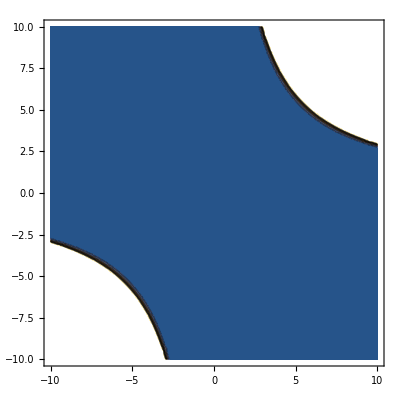

```mathematica
ContourPlot[Exp[x y],{x,-10, 10},{y,-10, 10}]
```

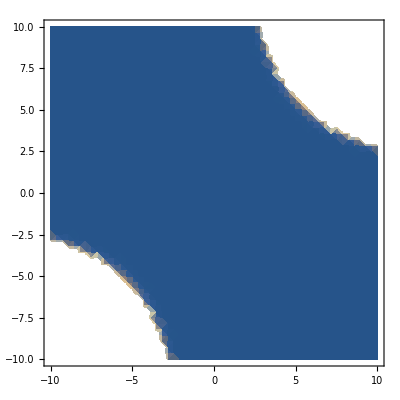

```mathematica
DensityPlot[Exp[x y],{x,-10, 10},{y,-10, 10}]
```

### 3D Plots

```mathematica
?Plot3D
```

```mathematica
Plot3D[Sin[t]Cos[u],{u,-3, 3}, {t,-3,3}]
```

-Graphics3D-

```mathematica
?ParametricPlot3D
```

Let’s Plot Helix

```mathematica
ParametricPlot3D[{t/10,Cos[t],Sin[t]}, {t, 0, 20Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t/15, Exp[-t/100]Cos[t], Exp[-t/100]Sin[t]}, {t, 0, 20Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t/5 Exp[-t/100],Cos[t],Sin[t]}, {t, 0, 20Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t]Cos[u],Sin[t]Sin[u],Cos[t]}, {t, 0, Pi}, {u,0,2Pi}]
```

-Graphics3D-

## Complex Numbers

So till now our discussion didn’t involve any calculation related to Complex numbers, we know that these class of numbers are also very important, let’s explore explore some functions related to that

```mathematica
z = 3 + 4I
```

3+4 ⅈ

```mathematica
Re[z]
```

3

```mathematica
Im[z]
```

4

```mathematica
Conjugate[z]
```

3-4 ⅈ

```mathematica
Abs[z]
```

5

```mathematica
Arg[z]
```

ArcTan[4/3]

```mathematica
z=(x +I y)^2
```

(x+ⅈ y)^2

```mathematica
ComplexExpand[z]
```

x^2+2 ⅈ x y-y^2

```mathematica
ComplexExpand[z,{x,y}]
```

-Im[x]^2+Im[y]^2-2 Im[y] Re[x]+Re[x]^2-2 Im[x] Re[y]-Re[y]^2+ⅈ (-2 Im[x] Im[y]+2 Im[x] Re[x]-2 Im[y] Re[y]+2 Re[x] Re[y])

Let’s take an example from wave optics, The N slit intensity can be written as ∑_(k=0)^(N-1) e^(i j ϕ)

```mathematica
Amp[N_,ϕ_] = Sum[Exp[I k ϕ],{k,0,N-1}] (*use "esc phi esc" to write ϕ and this works for any symbol*)
```

(-1+ⅇ^(ⅈ N ϕ))/(-1+ⅇ^(ⅈ ϕ))

```mathematica
Astar[N_,ϕ_]:= Assuming[{ϕ∈Reals,N∈Reals},Simplify[Conjugate[ComplexExpand[Amp[N,ϕ]]]]]
```

Don’t panic I have used Assuming function for just letting Mathematica know that ϕ, N ∈ ℝ

```mathematica
Int= Simplify[A[N,ϕ] Astar[N,ϕ]]
```

Csc[ϕ/2]^2 Sin[(N ϕ)/2]^2

```mathematica
Intensity[N_,ϕ_]:=A[N,ϕ] Astar[N,ϕ]
```

We have got the intensity, and ϕ = ((2π)/λ) d sin(θ), let’s plot the Intensity in a 2 slit arrangement

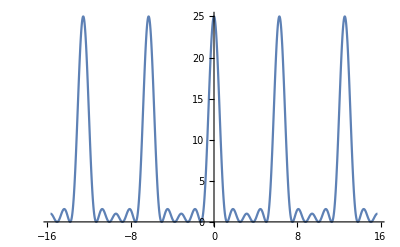

```mathematica
Plot[Intensity[5,phi],{phi, -5Pi, 5Pi}]
```

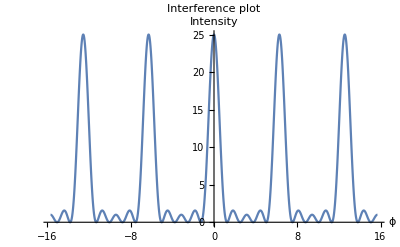

```mathematica
Show[%74,AxesLabel->{HoldForm[ϕ],HoldForm[Intensity]},PlotLabel->HoldForm[Interference plot],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## Animation using Mathematica

If you ever tried to create an animation with python or any programming language then you would know how tough it is, one of the most powerful feature of Mathematica is the ease with which animations can be achieved.

```mathematica
?Animate
```

Let’s animate a simple wave using the wave equation (∂^2 ψ)/(∂t^2) = (∂^2 ψ)/(∂x^2)

```mathematica
ψ[x_,t_]:=Sin[-x+t] (*Simplest solution to the wave equation*)
```

```mathematica
Animate[Plot[ψ[x,t],{x,0,10}] ,{t,0,10,0.01}]
```

```mathematica
Animate[Plot3D[Cos[-x +t],{x,0,2Pi},{y,0,2Pi}],{t,0,2Pi}]
```

## Here we conclude our first chapter.